```mathematica
getImageData[image_] := ImageData[image,"Byte"];
```

```mathematica
imageFromData[data_]:=Image[data,"Byte"];
```

```mathematica
convertToYCbCr[{R_,G_,B_}]:=Module[{Y,Cr,Cb},
({{Y}, {Cb}, {Cr}})=({{0}, {128}, {128}})+({{0.299, 0.587, 0.114}, {-0.169, -0.331, 0.500}, {0.500, -0.419, -0.081}}).({{R}, {G}, {B}});
{Y,Cb,Cr}
];
```

```mathematica
convertFromYCbCr[{Y_,Cb_,Cr_}]:=Module[{R,G,B},
({{R}, {G}, {B}})=({{1.000, 0.000, 1.400}, {1.000, -0.343, -0.711}, {1.000, 1.765, 0.000}}).({{Y}, {Cb-128}, {Cr-128}});
{R,G,B} // IntegerPart
];
```

```mathematica
getRGB[imageData_] := Flatten[imageData,{{3}, {1}, {2}}];
```

```mathematica
combineColor[r_]:=Flatten[r,{{2},{3},{1}}];
```

```mathematica
getTransformants[layer_] := Partition[layer, {8,8},8,{1,1},{-1}];
```

```mathematica
mergeTransformants[layer_] := Flatten[layer, {{1,3},{2,4}}];
```

```mathematica
Clear[normalize]
normalize[t_]:=t/;t[[-1,-1]] ≠ -1; 
normalize[t_]:=Block[{f, result = t, last},(
f[row_]:=row/; First@row == -1 || Last@row≠-1; 
f[row_]:=row /. -1 -> (TakeWhile[row,NonNegative] // Last);

result = f /@ result;
result = Flatten[result,{{2},{1}}];
result = f /@ result;
result = Flatten[result, {{2},{1}}];

result
)];
```

```mathematica
restructure[t_] := FourierDCT[t] // IntegerPart;
```

```mathematica
reverseDCT[t_] := FourierDCT[t,3] ;
```

```mathematica
Clear[Quant]
Quant[s_]:= Quant[s]= Table[1+(1+(i-1)+(j-1))*s,{i,1,8},{j,1,8}];
```

```mathematica
quantize[t_, s_] := Quotient[t,Quant[s]];
```

```mathematica
dequantize[t_, s_] := Times[t,Quant[s]];
```

```mathematica
removeSigns[t_] := Abs[t];
```

```mathematica
signs[t_] := Positive[t] /.{True -> 1, False ->0};
```

```mathematica
applySigns[numbers_,signs_]:= Times[numbers,Replace[signs,0->-1,2]];
```

```mathematica
Clear[fromBits]
fromBits[b_]:=fromBits[b] = FromDigits[Reverse@b,2];
```

```mathematica
Clear[bitcube];
bitcube[t_]:=Block[{result = t}, (
result = IntegerDigits[t,2]//PadLeft;
result = Flatten[result,{{3},{1,2}}] // Reverse;

result
)];
```

```mathematica
foldCube[sequences_]:=Block[{planes, cube, result},(
planes = (Partition[#,√Length[#]])&/@ sequences;
cube = Flatten[planes,{{2},{3},{1}}];
result = Map[fromBits,cube,{2}];

result
)];
```

```mathematica
Clear[compressBits];
compressBits[bits_] := compressBits[bits] = Length /@ ({0,bits}//Flatten //Split);
```

```mathematica
Clear[decompressBits,unfoldSerie];
unfoldSerie[n_Integer,{_?EvenQ}] :=ConstantArray[1.,n];
unfoldSerie[n_Integer,{_?OddQ}] :=ConstantArray[0.,n];
decompressBits[s_]:=decompressBits[s]=MapIndexed[unfoldSerie,s] //Flatten//Rest;
```

```mathematica
Options[Quantize] = {useQuantizeLevel->0};
compressTransformant[t_] := Module[{result = t, signsMatrix, quantizeLevel},(
result = normalize[result];
result = restructure[result];

quantizeLevel = OptionValue[Quantize,useQuantizeLevel];
result = quantize[result, quantizeLevel];

signsMatrix = signs[result];
result = removeSigns[result];
result = bitcube[result];
result = compressBits /@ result;

{result,signsMatrix}
)];
```

```mathematica
decompressTransformant[{r_,s_}] := Module[{result = r, quantizeLevel}, (
result=decompressBits /@ result;
result=foldCube[result];
result=applySigns[result,s];

quantizeLevel = OptionValue[Quantize,useQuantizeLevel];
result= dequantize[result, quantizeLevel];


result=reverseDCT[result];

result
)];
```

```mathematica
compress[image_] := Module[{result =image,dimensions = ImageDimensions[image]},(
result = getImageData[result];
result = Map[convertToYCbCr,result, {2}];
result = getRGB[result];
result = getTransformants /@ result;
result = Map[compressTransformant,result,{3}];

{dimensions,result}
)];
```

```mathematica
decompress[{dimensions_,r_}] := Module[{result =r},(
result = Map[decompressTransformant, result,{3}];
result = mergeTransformants /@ result;
result = combineColor[result];
result = Map[convertFromYCbCr,result,{2}];
result = imageFromData[result];
result = ImageCrop[result,dimensions,{Right, Bottom}];
result
)];
```

```mathematica
sko[image_,retoredImage_] := Module[{data, restoredData, result,f}, (
data = getImageData[image] // getRGB;
restoredData = getImageData[restoredImage] // getRGB;

result = {data, restoredData}; (*Images x Colors x Pixels x Pixels*)
result = Flatten[result, {{2},{1},{3,4}}]; (*Color x Images x Pixels*)
result = Flatten[result, {{1},{3},{2}}]; (*Color x Pixel x Images*)

f[{o_, r_}] := (o-r)^2 // N ; 
result = Map[f,result,{2}]; (*Color x Pixel diff *)
result = Map[(√((Plus@@#1)/Length[#1]))& ,result, {1}];
result // Mean // N
)];
```

```mathematica
path = SystemDialogInput["FileOpen"];
image = Import[path];
```

```mathematica
SetOptions[Quantize,useQuantizeLevel->0];
compressedImage = image // compress;
```

```mathematica
restoredImage = compressedImage // decompress;
```

```mathematica
image
restoredImage
ImageDifference[image,restoredImage]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
δ = sko[image,restoredImage]
h = 20 Log10[255/δ]
```

0.973936

48.3602

```mathematica
collectStats[{_,r_}, statFunction_]:=Module[{result = r, f},(
f[{t_,_}]:=  statFunction[ t];
result = Map[f,result,{3}]; (*Work with transformants*)
result =Flatten[result,{{1},{2,3}}];(*Combine transformant matrix*)
result
)];
```

```mathematica
statFromTransformant[t_] := t
```

```mathematica
stat = collectStats[compressedImage,statFromTransformant];
```

```mathematica
planes = (Reap[MapIndexed[Sow[#1,#2[[2]]]&,#, {2}]] // Last)& /@ stat;
```

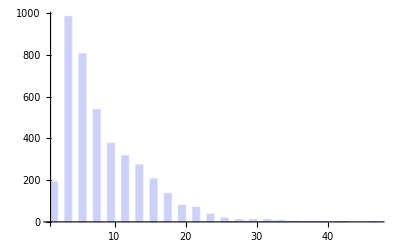
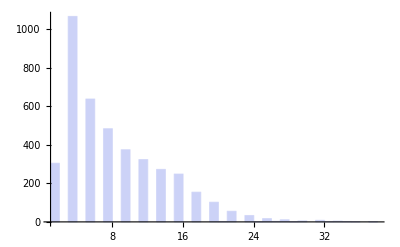
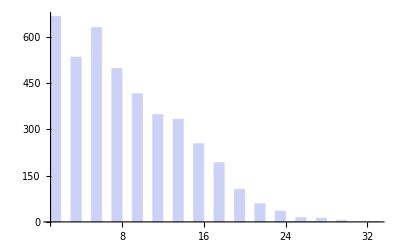
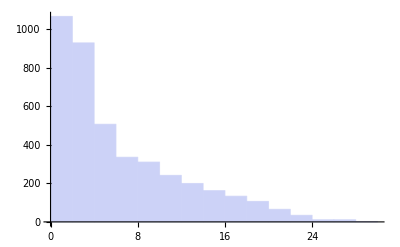
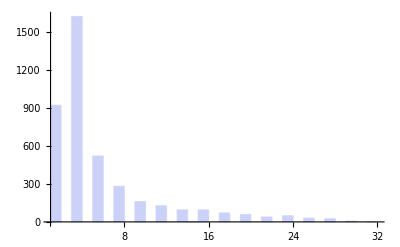
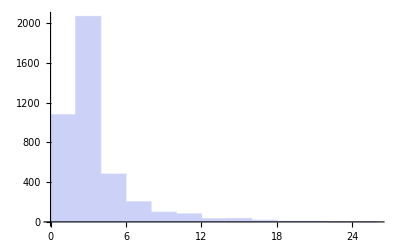
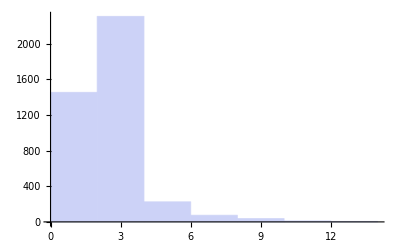
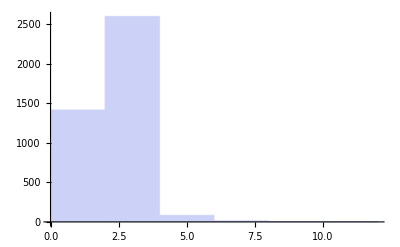
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Map[Histogram@(Length/@#)&,planes,{2}]
```